# Tarea3

El objetivo a este punto del proyecto es tratar de replicar y en base a eso mejorar los resultados del paper Alonso-Lobo para ambos casos de billares cuánticos simulados con caminatas cuántica (rectangular y de estadio) y verificar con una segunda distribución P(r) (sin unfolding)

Como en los casos anteriores definiremos los parámetro iniciales

```mathematica
mR=20;nU=10;         (*tamaño del medio*)    
alpha=Pi/4;beta=Pi/4;    
nbins=60;sMax=5;         
rBins=40;                  
useCircularSpacing=False;   (*Esto namas es para las graficas*)
```

Ahora empezaremos  a preparar los datos para realizar poder definir los operadores de desplazamiento.

```mathematica
posIndex[m_,n_]:=(n-1)*mR+m; 
globalIndex[m_,n_,spin_]:=2*(posIndex[m,n]-1)+If[spin=="U",1,2];
Ccoin[θ_]:={{Cos[θ],Sin[θ]}, (*matriz de moneda*){-Exp[I*Pi/4] Sin[θ],Exp[I*Pi/4] Cos[θ]}};
C1=Ccoin[alpha]; (*pasos horizontales y verticale*)
C2=Ccoin[beta];
Npos=mR*nU;dim=2*Npos; (*numero de posiciones del caminate*)
Ipos=IdentityMatrix[Npos,SparseArray];
```

Ahora haremos la construcción del operador de desplazamiento (en el rectángulo)

```mathematica
(*BuildRectWMWN[mR_,nU_]:=Module[{...},... {Wm,Wn}]*)
BuildRectWMWN[mR_,nU_]:=Module[{mVals,nVals,Uidx,Didx,targetU,targetD,rulesWm,Wm,targetU2,targetD2,rulesWn,Wn},mVals=Flatten@Table[m,{n,1,nU},{m,1,mR}]; (*todas las coordenadas*)
nVals=Flatten@Table[n,{n,1,nU},{m,1,mR}];
Uidx=globalIndex@@@ (*indices globales*)Transpose[{mVals,nVals,ConstantArray["U",Length[mVals]]}];
Didx=globalIndex@@@Transpose[{mVals,nVals,ConstantArray["D",Length[mVals]]}];
targetU= (*desplazamiento horizontal*)MapThread[If[#1<mR,globalIndex[#1+1,#2,"U"],globalIndex[mR,#2,"D"]]&,{mVals,nVals}];
targetD= (*desplzamiento vertical*)MapThread[If[#1>1,globalIndex[#1-1,#2,"D"],globalIndex[1,#2,"U"]]&,{mVals,nVals}];
rulesWm=Join[MapThread[{#1,#2}->1&,{targetU,Uidx}],MapThread[{#1,#2}->1&,{targetD,Didx}]];
Wm=SparseArray[rulesWm,{dim,dim}];targetU2=MapThread[If[#2<nU,globalIndex[#1,#2+1,"U"],globalIndex[#1,nU,"D"]]&,{mVals,nVals}];
targetD2=MapThread[If[#2>1,globalIndex[#1,#2-1,"D"],globalIndex[#1,1,"U"]]&,{mVals,nVals}];
rulesWn=Join[MapThread[{#1,#2}->1&,{targetU2,Uidx}],MapThread[{#1,#2}->1&,{targetD2,Didx}]];
Wn=SparseArray[rulesWn,{dim,dim}];
{Wm,Wn}] (*resultado de dos matrices*)
```

Definimos las funciones f que nos dan la frontera curvada, luego generaremos una lista de puntos dentro del estadio, los mapearemos a nuevos puntos  y crearemos los operadores de desplazamiento

```mathematica
BuildStadiumWMWN[mR_,nU_]:=Module[{mVals,nVals,validPoints,posToIndex,totalPoints,globalStIndex,targetU,targetD,rulesWm,rulesWn,Wm,Wn,isInside,mMax,nMax},mMax=mR; (*valores de frontera*)
nMax=nU;
isInside[m_,n_]:=Module[{center,radius},center=mR/2;
radius=nU/2;
If[m<=mR&&m>=1,If[m<center,(m-center)^2+(n-nU/2)^2<=(radius)^2,True],False]];
validPoints= (*puntos dento del estadio*)Select[Flatten[Table[{m,n},{m,1,mMax},{n,1,nMax}],1],isInside[#[[1]],#[[2]]]&];
totalPoints=Length[validPoints];
posToIndex=AssociationThread[validPoints->Range[totalPoints]];
globalStIndex[m_,n_,spin_]:=2*(posToIndex[{m,n}]-1)+If[spin=="U",1,2];
targetU={}; (*contruccion del operador de evolución*)
targetD={};
rulesWm={};
rulesWn={};
Do[If[KeyExistsQ[posToIndex,{m+1,n}],AppendTo[rulesWm,{globalStIndex[m+1,n,"U"],globalStIndex[m,n,"U"]}->1],AppendTo[rulesWm,{globalStIndex[m,n,"D"],globalStIndex[m,n,"U"]}->1]];
If[KeyExistsQ[posToIndex,{m-1,n}],AppendTo[rulesWm,{globalStIndex[m-1,n,"D"],globalStIndex[m,n,"D"]}->1],AppendTo[rulesWm,{globalStIndex[m,n,"U"],globalStIndex[m,n,"D"]}->1]];
If[KeyExistsQ[posToIndex,{m,n+1}],AppendTo[rulesWn,{globalStIndex[m,n+1,"U"],globalStIndex[m,n,"U"]}->1],AppendTo[rulesWn,{globalStIndex[m,n,"D"],globalStIndex[m,n,"U"]}->1]];
If[KeyExistsQ[posToIndex,{m,n-1}],AppendTo[rulesWn,{globalStIndex[m,n-1,"D"],globalStIndex[m,n,"D"]}->1],AppendTo[rulesWn,{globalStIndex[m,n,"U"],globalStIndex[m,n,"D"]}->1]];,{m,1,mMax},{n,1,nMax}];
Wm=SparseArray[rulesWm,{2*totalPoints,2*totalPoints}];
Wn=SparseArray[rulesWn,{2*totalPoints,2*totalPoints}];
<|"Wm"->Wm,"Wn"->Wn,"posToIndex"->posToIndex,"validPoints"->validPoints|>]
```

Ahora podemos construir  la moneda tomando en cuenta todas las posiciones

```mathematica
MakeCoinTotalRect[alpha_,beta_]:=Module[{C1t,C2t},C1t=KroneckerProduct[Ccoin[alpha],IdentityMatrix[Npos,SparseArray]];
C2t=KroneckerProduct[Ccoin[beta],IdentityMatrix[Npos,SparseArray]];
{C1t,C2t}];
```

Ahora podemos diagonalizar los eigenvectores

```mathematica
ClearAll[GetEigenPhases]
GetEigenPhases[Umat_,opts___]:=Module[{evals,phases},Print["Diagonalizing matrix of dimension: ",Dimensions[Umat][[1]]];
evals=Quiet[Eigenvalues[Normal[Umat]]];(*conversión explícita y silenciosa*)phases=Mod[Arg[evals],2 Pi];
Sort[phases]]



(*GetEigenPhases[Umat_,opts___]:=Module[{evals,phases},Print["Di ",Dimensions[Umat][[1]]];
evals=Eigenvalues[Umat, (*calculo de eigenvevalores*)Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->100000}];
phases=Mod[Arg[evals],2 Pi]; (*fases de los eigenvalores*)
(*Ordena las fases*)Sort[phases]]
(*GetEigenPhases[Umat_,opts...]:=Module[...]*)*)
```

Ahora ya podemos empezar a construir el unfolding

```mathematica
UnfoldSimple[phs_List,includeCircular_:False]:= (*primero ordenamos las fases*)Module[{sorted,diffs,sNorm},sorted=Sort[phs];
diffs=Differences[sorted];
(*circular:espacio entre el último y el primero*)If[includeCircular,diffs=Append[diffs,2 Pi-Last[sorted]+First[sorted]];];
(*se calcula el promedio para porder normalizar*)sNorm=diffs/Mean[diffs];
sNorm] (*espaciamientos normalizados*)


UnfoldSpline[phs_List]:= (*Ahora haremos un reescalamiento para tener que el unfolding sea una densidada normalizada y local, no como el paper que tiene una variación "lenta", o sea solo dejamos las fluctuaciones locales*)Module[{sorted,nLevels,cumulative,fit,unfolded,diffs,sNorm},(*Ordena las fases*)sorted=Sort[phs];
nLevels=Range[Length[sorted]];
cumulative=Transpose[{sorted,nLevels}];(*acumulador*)
fit=Interpolation[cumulative,Method->"Spline"];(*reescalador*)
unfolded=fit/@sorted;
diffs=Differences[unfolded]; (*calculo de espaciamientos*)
sNorm=diffs/Mean[diffs];
sNorm] (*espaciamientos normalizados*)
```

Calcularemos ahora los espaciamientos consecutivos midiendo la correlación con los vecinos (esto es para ya no usar el unfolding, para verificar RMT)

```mathematica
ClearAll[PRatiosFromPhases]
PRatiosFromPhases[phs_List,includeCircular_:False]:=Module[{sorted,sp,spAll,r},sorted=Sort[phs];
sp=Differences[sorted]; (*ordenamos*)
(*Print[sp];*)
If[includeCircular&&Length[sorted]>=2,sp=Append[sp,2 Pi-Last[sorted]+First[sorted]];]; (*espaciamiento circular*)
If[Length[sp]<2,Return[{}]]; (*en caso de no tener datos en la lista solo la devuelve vacía para no entrar en bucles infinitos*)
r=Table[Min[sp[[i]],sp[[i-1]]]/Max[sp[[i]],sp[[i-1]]],{i,2,Length[sp]}]; (*r_i=min(s_i,s_{i-1})/max(s_i,s_{i-1}) *)
r]
```

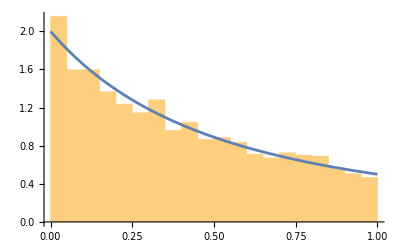

```mathematica
Show[
Histogram[PRatiosFromPhases[RandomReal[{-1,1},4000]],Automatic,"PDF"],
Plot[2/(1+r)^2,{r,0,1}]
]
```

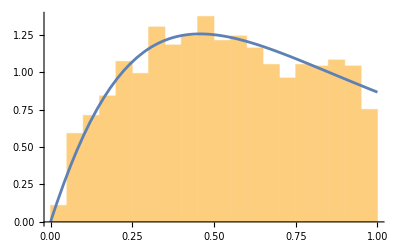

```mathematica
Show[
Histogram[PRatiosFromPhases[Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[2000]]]],Automatic,"PDF"],
Plot[27(r+r^2)/(4(1+r+r^2)^(5/2)),{r,0,1}]
]
```

Ahora encontraremos el operador de evolución, calculando las eigenfases, aplicando el unfolding y las distribuciones para realizar las graficas

```mathematica
exportFolder="figs/";
```

```mathematica
ClearAll[AnalyzeSystem]
AnalyzeSystem[systemName_String,Wm_,Wn_,C1t_,C2t_,opts___]:=Module[{Ustep,dimU,phases,sSimple,sSpline,rList,poissonPs,wignerPs,poissonPr,wignerPr,hPsSimple,hPsSpline,hPr,exportPathPsSimple,exportPathPsSpline,exportPathPr},Print["\n=== Analizando sistema: ",systemName," ==="];
Ustep=Wn.C2t.Wm.C1t;(*operador de evolución*)
dimU=Dimensions[Ustep][[1]];
Print["Tamaño de matriz U: ",dimU];
Print["Esto es para verificar la unitariedad"];
Print["‖U†U - I‖ = ",Norm[Chop[Ustep.ConjugateTranspose[Ustep]-IdentityMatrix[dimU]]]];
phases=GetEigenPhases[N@Ustep]; (*Diagonalizamos*)
Print["Número de eigenfases obtenidas: ",Length[phases]];
sSimple=UnfoldSimple[phases]; (*P(s)*)
Print["sSimple"];
(*sSpline=UnfoldSpline[phases];*)
Print["sSpimple"];
(*rList=PRatiosFromPhases[phases]; (*P(r)*)*)
Print["rList"];
poissonPs[s_]:=Exp[-s];
wignerPs[s_]:=(Pi s/2) Exp[-Pi s^2/4];
poissonPr[r_]:=2/(1+r)^2;
wignerPr[r_]:=(27/8) ((r+r^2)/(1+r+r^2)^(5/2));
(*A partir de aquí van las figuras*)
exportPathPsSimple=FileNameJoin[{exportFolder,"QW_"<>systemName<>"_Ps_simple.png"}];
exportPathPsSpline=FileNameJoin[{exportFolder,"QW_"<>systemName<>"_Ps_spline.png"}];
exportPathPr=FileNameJoin[{exportFolder,"QW_"<>systemName<>"_Pr.png"}];
hPsSimple=Show[Histogram[sSimple,Automatic,"PDF"(*{0,4,0.1},"Probability"*),PlotRange->All,ChartStyle->Directive[Opacity[0.5],Blue],Frame->True,FrameLabel->{"s","P(s)"},PlotLabel->"P(s) - "<>systemName<>" (Unfold Simple)"],Plot[{poissonPs[s],wignerPs[s]},{s,0,4},PlotLegends->{"Poisson","Wigner"},PlotStyle->{{Red,Dashed},{Green,Thick}}]];
Export[exportPathPsSimple,hPsSimple];
(*hPsSpline=Show[Histogram[sSpline,{0,4,0.1},"Probability",PlotRange->All,ChartStyle->Directive[Opacity[0.5],Blue],Frame->True,FrameLabel->{"s","P(s)"},PlotLabel->"P(s) - "<>systemName<>" (Unfold Spline)"],Plot[{poissonPs[s],wignerPs[s]},{s,0,4},PlotLegends->{"Poisson","Wigner"},PlotStyle->{{Red,Dashed},{Green,Thick}}]];
Export[exportPathPsSpline,hPsSpline];*)
(*hPr=Show[Histogram[rList,{0,1,0.05},"Probability",ChartStyle->Directive[Opacity[0.5],Blue],Frame->True,FrameLabel->{"r","P(r)"},PlotLabel->"P(r) - "<>systemName],Plot[{poissonPr[r],wignerPr[r]},{r,0,1},PlotLegends->{"Poisson","Wigner"},PlotStyle->{{Red,Dashed},{Green,Thick}}]];
Export[exportPathPr,hPr];*)
(*---8. Reporte de resultados---*)Print["Figuras exportadas en: ",exportFolder];
Print["--- Resumen ---"];
(*Print["<s> Simple: ",Mean[sSimple],"   <s> Spline: ",Mean[sSpline]]*);
(*Print["<r>: ",Mean[rList]];*)
<|"phases"->phases,"sSimple"->sSimple,(*"sSpline"->sSpline,*)(*"rList"->rList*)|>]
```

Ahora podemos construir los operadores de moneda y billar

```mathematica
Print["\n=== RECTÁNGULO ==="];

(*desplazamientos y coins*)
{WmRect,WnRect}=BuildRectWMWN[mR,nU];
{C1totRect,C2totRect}=MakeCoinTotalRect[alpha,beta];

(*Ejecutar análisis espectral completo*)
resRect=AnalyzeSystem["Rectangle",WmRect,WnRect,C1totRect,C2totRect];
```

=== RECTÁNGULO ===

=== Analizando sistema: Rectangle ===

Tamaño de matriz U: 400

Esto es para verificar la unitariedad

‖U†U - I‖ = 0

Diagonalizing matrix of dimension: 400

Número de eigenfases obtenidas: 400

sSimple

sSpimple

rList

Figuras exportadas en: figs/

--- Resumen ---

## Billar de rectángulo

```mathematica
BuildStadiumWMWN[mR_,nU_]:=Module[{mVals,nVals,validPoints,posToIndex,totalPoints,globalStIndex,targetU,targetD,rulesWm,rulesWn,Wm,Wn,isInside,mMax,nMax},mMax=mR; (*valores de frontera*)
nMax=nU;
isInside[m_,n_]:=Module[{center,radius},center=mR/2;
radius=nU/2;

If[m<=mR&&m>=1,If[m<center,(m-center)^2+(n-nU/2)^2<=(radius)^2,True],False]];

validPoints= (*puntos dento del estadio*)Select[Flatten[Table[{m,n},{m,1,mMax},{n,1,nMax}],1],isInside[#[[1]],#[[2]]]&];
Print[validPoints];
totalPoints=Length[validPoints];
posToIndex=AssociationThread[validPoints->Range[totalPoints]];
globalStIndex[m_,n_,spin_]:=2*(posToIndex[{m,n}]-1)+If[spin=="U",1,2];
targetU={}; (*contruccion del operador de evolución*)
targetD={};
rulesWm={};
rulesWn={};
Print["Hasta aquí bien"];
Do[
Print[Max[Select[validPoints,#[[1]]==m&][[All,2]]]];
If[KeyExistsQ[posToIndex,{m+1,n}],AppendTo[rulesWm,{globalStIndex[m+1,n,"U"],globalStIndex[m,n,"U"]}->1],AppendTo[rulesWm,{globalStIndex[m,n,"D"],globalStIndex[m,n,"U"]}->1]];
If[KeyExistsQ[posToIndex,{m-1,n}],AppendTo[rulesWm,{globalStIndex[m-1,n,"D"],globalStIndex[m,n,"D"]}->1],AppendTo[rulesWm,{globalStIndex[m,n,"U"],globalStIndex[m,n,"D"]}->1]];
If[KeyExistsQ[posToIndex,{m,n+1}],AppendTo[rulesWn,{globalStIndex[m,n+1,"U"],globalStIndex[m,n,"U"]}->1],AppendTo[rulesWn,{globalStIndex[m,n,"D"],globalStIndex[m,n,"U"]}->1]];
If[KeyExistsQ[posToIndex,{m,n-1}],AppendTo[rulesWn,{globalStIndex[m,n-1,"D"],globalStIndex[m,n,"D"]}->1],AppendTo[rulesWn,{globalStIndex[m,n,"U"],globalStIndex[m,n,"D"]}->1]];,{m,1,mMax},{n,1,Max[Select[validPoints,#[[1]]==m&][[All,2]]]}];
Wm=SparseArray[rulesWm,{2*totalPoints,2*totalPoints}];
Wn=SparseArray[rulesWn,{2*totalPoints,2*totalPoints}];
<|"Wm"->Wm,"Wn"->Wn,"posToIndex"->posToIndex,"validPoints"->validPoints|>]
```

```mathematica
{Wm,Wn}={BuildStadiumWMWN[3,3]["Wm"],BuildStadiumWMWN[3,3]["Wn"]}
```

{{1,1},{1,2},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

Hasta aquí bien

2

2

3

3

3

«3 more identical outputs»

{{1,1},{1,2},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

Hasta aquí bien

2

2

3

3

3

«3 more identical outputs»

{SparseArray[…],SparseArray[…]}

```mathematica
UnitaryMatrixQ/@{Wm,Wn}
```

{True,True}

```mathematica
{mR,nU}
```

{20,10}

```mathematica
BuildStadiumWMWN[6,4]
```

{{1,2},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{6,1},{6,2},{6,3},{6,4}}

Hasta aquí bien

2

2

3

3

3

4

4

4

«13 more identical outputs»

SparseArray::posd: The left-hand side of {3,1+2 (-1+Missing[KeyAbsent,{1,1}])}→1 in … is not a position or a pattern that will match the position of an element in an array with dimensions {40,40}.

SparseArray::posd: The left-hand side of {1,1+2 (-1+Missing[KeyAbsent,{1,1}])}→1 in … is not a position or a pattern that will match the position of an element in an array with dimensions {40,40}.

<|Wm→SparseArray[{{3,1+2 (-1+Missing[KeyAbsent,{1,1}])}→1,{1+2 (-1+Missing[KeyAbsent,{1,1}]),2+2 (-1+Missing[KeyAbsent,{1,1}])}→1,{5,1}→1,{1,2}→1,{9,3}→1,{3,4}→1,{11,5}→1,{2,6}→1,{13,7}→1,{7,8}→1,{17,9}→1,{4,10}→1,{19,11}→1,{6,12}→1,{21,13}→1,{8,14}→1,{23,15}→1,{15,16}→1,{25,17}→1,{10,18}→1,{27,19}→1,{12,20}→1,{29,21}→1,{14,22}→1,{31,23}→1,{16,24}→1,{33,25}→1,{18,26}→1,{35,27}→1,{20,28}→1,{37,29}→1,{22,30}→1,{39,31}→1,{24,32}→1,{34,33}→1,{26,34}→1,{36,35}→1,{28,36}→1,{38,37}→1,{30,38}→1,{40,39}→1,{32,40}→1},{40,40}],Wn→SparseArray[{{1,1+2 (-1+Missing[KeyAbsent,{1,1}])}→1,{1+2 (-1+Missing[KeyAbsent,{1,1}]),2+2 (-1+Missing[KeyAbsent,{1,1}])}→1,{2,1}→1,{1,2}→1,{5,3}→1,{3,4}→1,{7,5}→1,{4,6}→1,{8,7}→1,{6,8}→1,{11,9}→1,{9,10}→1,{13,11}→1,{10,12}→1,{15,13}→1,{12,14}→1,{16,15}→1,{14,16}→1,{19,17}→1,{17,18}→1,{21,19}→1,{18,20}→1,{23,21}→1,{20,22}→1,{24,23}→1,{22,24}→1,{27,25}→1,{25,26}→1,{29,27}→1,{26,28}→1,{31,29}→1,{28,30}→1,{32,31}→1,{30,32}→1,{35,33}→1,{33,34}→1,{37,35}→1,{34,36}→1,{39,37}→1,{36,38}→1,{40,39}→1,{38,40}→1},{40,40}],posToIndex→<|{1,2}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,1}→5,{3,2}→6,{3,3}→7,{3,4}→8,{4,1}→9,{4,2}→10,{4,3}→11,{4,4}→12,{5,1}→13,{5,2}→14,{5,3}→15,{5,4}→16,{6,1}→17,{6,2}→18,{6,3}→19,{6,4}→20|>,validPoints→{{1,2},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{6,1},{6,2},{6,3},{6,4}}|>

```mathematica
(*desplazamientos y coins*)
{WmRect,WnRect}=BuildStadiumWMWN[mR,nU];
{C1totRect,C2totRect}=MakeCoinTotalRect[alpha,beta];
```

{{5,5},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10}}

Hasta aquí bien

Do::iterb: Iterator {n,1,Max[Select[validPoints$623339,Slot[«1»]⟦1⟧==m&]⟦All,2⟧]} does not have appropriate bounds.

Set::shape: Lists {WmRect,WnRect} and … are not the same shape.